```mathematica
(*Quit[]*)
```

Here, we consider the qualitative behaviour of the antagonistic specialization system when generalist payoff exceeds specialist payoff. First, we’ll consider the frequency of each strategist over time.

```mathematica
ANT[α_,αg_,fα_,γ_,x_]:= {u'[t]==-x (fα-α) γ (-1+u[t]) u[t] (v1[t]-v2[t]),v1'[t]== x γ v1[t] (fα-αg-fα v1[t]+αg v1[t]+fα u[t] (-1+v1[t]-v2[t])-α v2[t]+αg v2[t]+α u[t] (1-v1[t]+v2[t])),v2'[t]== -x γ v2[t] (-αg (-1+v1[t]+v2[t])+α (-1+u[t]+u[t] v1[t]+v2[t]-u[t] v2[t])+fα (v1[t]+u[t] (-1-v1[t]+v2[t]))), v1[0]==v10,v2[0]==v20,u[0]==u0}
```

Now we’ll plot this system, while first just varying the initial frequency of the symbiont. We’ll begin with intermediate frequencies of all host types:

```mathematica
PA=ANT[0.8,0.4,0.2,1,0.5];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,3000},{u0, v10, v20}];
ICs=Table[{u0,v10,v20},{u0,0.005,0.995,0.09}, {v10,{0.33}},{v20,{0.33}}]~Flatten~2;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Check the upper and lower bounds for stable symbionts:

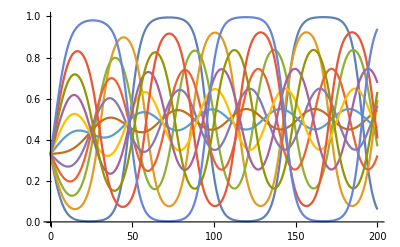

```mathematica
Plot[{v1series},{t,0,200},PlotRange -> {0,1}]
```

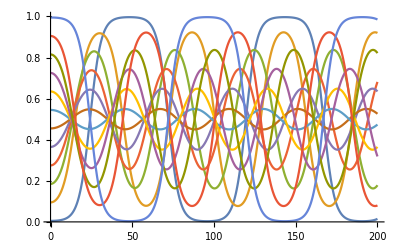

```mathematica
Plot[{useries},{t,0,200},PlotRange -> {0,1}]
```

This this system results in a limit cycle regardless of the initial frequency of the symbiont. Next, I’ll show that the generalist host always goes extinct when its payoff is lower than the specialist average:

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[1000]+v2[1000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{}

The generalist goes extinct, there are no cases in which the population is not entirely composed of the specialist.

Now we will hold symbiont frequency steady and vary the initial frequency of only host 1:

```mathematica
PA=ANT[0.8,0.4,0.2,1,0.5];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,0.005,0.995,0.09},{v20,{0.33}}, {vg0,{0.33}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Now we’ll plot the frequency of hosts:

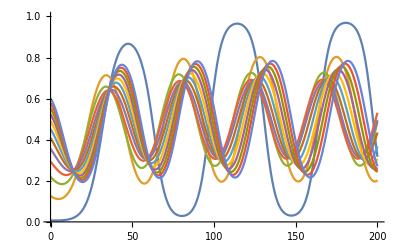

```mathematica
Plot[{v1series},{t,0,200},PlotRange -> {0,1}]
```

And here we’ll plot the frequency of symbionts:

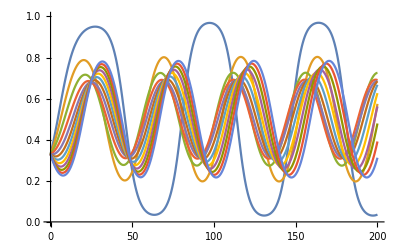

```mathematica
Plot[{useries},{t,0,200},PlotRange -> {0,1}]
```

So any initial frequency of host 1 leads to a limit cycle.

We’ll check our result that generalists go extinct:

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[1000]+v2[1000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{}

As expected the generalists are excluded from the limit cycle. Next we vary the initial frequency of symbiont 2:

```mathematica
PA=ANT[0.8,0.4,0.2,1,0.5];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,10000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,{0.33}},{v20,0.005,0.995,0.09}, {vg0,{0.33}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Now we’ll plot the frequency of hosts:

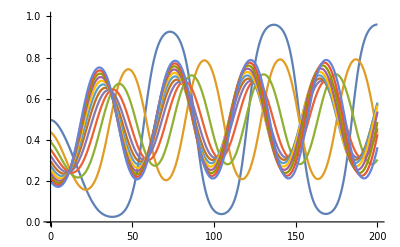

```mathematica
Plot[{v1series},{t,0,200},PlotRange -> {0,1}]
```

Next the symbionts:

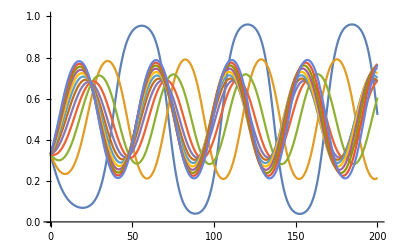

```mathematica
Plot[{useries},{t,0,200},PlotRange -> {0,1}]
```

Once more we’ll check the frequency of generalists:

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[1000]+v2[1000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{}

As before generalists go extinct.

Finally, we’ll test the extreme cases when one match or mismatch is extremely likely to fix. These occur when generalists are nearly entirely absent, and hosts and symbiont parings are extremely frequent or infrequent:

```mathematica
PA=ANT[0.8,0.4,0.2,1,0.5];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.005,0.995}}, {v10,{0.005,0.995}},{v20,{0.005,0.995}}, {vg0,{0.005}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

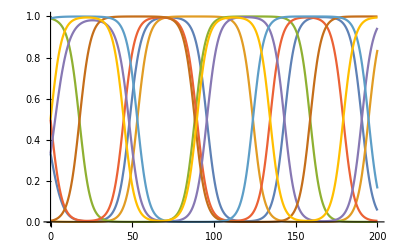

```mathematica
Plot[{v1series},{t,0,200},PlotRange -> {0,1}]
```

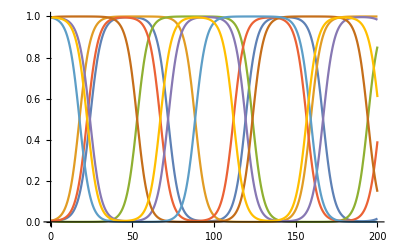

```mathematica
Plot[{useries},{t,0,200},PlotRange -> {0,1}]
```

These cases too result in limit cycles. Let’s check the frequency of generalists.

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[1000]+v2[1000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{}

As before the generalists go extinct, all remaining hosts are specialists of one type or another.

What happens when (π+π’)/2< π_g? Our stability analysis tells us that all hosts will be generalists.

Well first explore this case while varying initial symbiont frequency:

```mathematica
PA=ANT[0.8,0.8,0.2,1,0.5];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,3000},{u0, v10, v20}];
ICs=Table[{u0,v10,v20},{u0,0.005,0.995,0.09}, {v10,{0.33}},{v20,{0.33}}]~Flatten~2;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

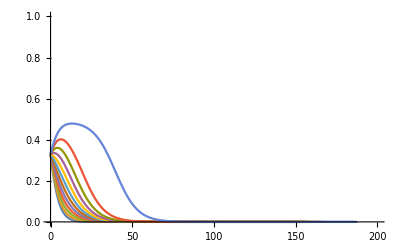

```mathematica
Plot[{v1series},{t,0,200},PlotRange -> {0,1}]
```

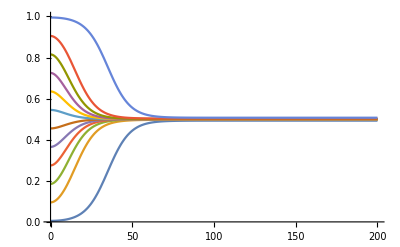

```mathematica
Plot[{useries},{t,0,200},PlotRange -> {0,1}]
```

The generalist always fixes, and an intermediate symbiont frequency remains.

Now we’ll vary the initial frequency of host 1:

```mathematica
PA=ANT[0.8,0.6,0.2,1,0.5];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,0.005,0.995,0.09},{v20,{0.05}},{vg0,{0.05}} ]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

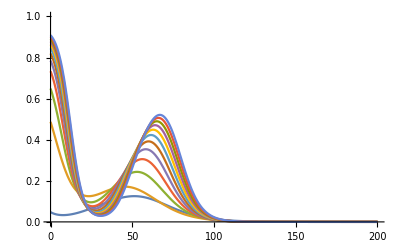

```mathematica
Plot[{v1series},{t,0,200},PlotRange -> {0,1}]
```

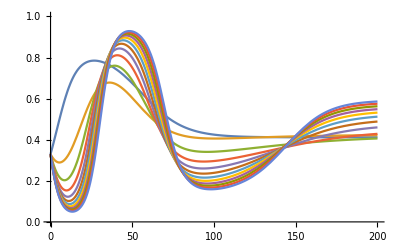

```mathematica
Plot[{useries},{t,0,200},PlotRange -> {0,1}]
```

The symbiont frequency fixes at some stable intermediate value, while all specialist hosts go extinct.

The same occurs in the case in which the frequency of the other specialist host varies.

Finally we consider the cases that are highly favourable to fixation of the specialist, even when generalist payoff exceeds their own:

```mathematica
PA=ANT[0.8,0.6,0.2,1,0.5];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.005,0.995}}, {v10,{0.005,0.995}},{v20,{0.005,0.995}},{vg0,{0.005}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

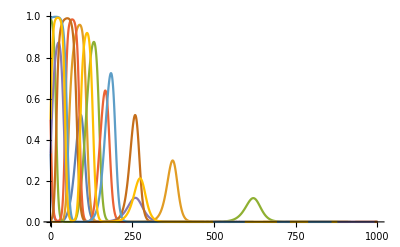

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

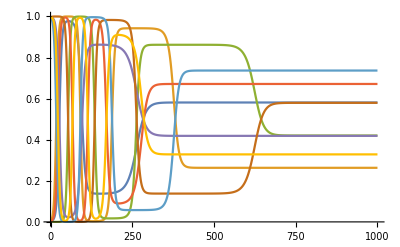

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```